String Patterns and Templates

String patterns work very much like other patterns in the Wolfram Language, except that they operate on sequences of characters in strings rather than parts of expressions. In a string pattern, you can combine pattern constructs like _ with strings like "abc" using ~~.

This picks out all instances of + followed by a single character:

```mathematica
StringCases["+string +patterns are +quite +easy", "+"~~_]
```

{+s,+p,+q,+e}

This picks out three characters after each +:

```mathematica
StringCases["+string +patterns are +quite +easy", "+"~~_~~_~~_]
```

{+str,+pat,+qui,+eas}

Use the name x for the character after each +, and return that character framed:

```mathematica
StringCases["+string +patterns are +quite +easy", "+"~~x_->Framed[x]]
```

{s,p,q,e}

In a string pattern, _ stands for any single character. _ _ (“double blank”) stands for any sequence of one or more characters, and _ _ _ (“triple blank”) stands for any sequence of zero or more characters. _ _ and _ _ _ will normally grab as much of the string as they can.

Pick out the sequence of characters between [ and ]:

```mathematica
StringCases["the [important] word", "["~~x__~~"]"->Framed[x]]
```

{important}

_ _ normally matches as long a sequence of characters as it can:

```mathematica
StringCases["now [several] important [words]", "["~~x__~~"]"->Framed[x]]
```

{several] important [words}

Shortest forces the shortest match:

```mathematica
StringCases["now [several] important [words]", "["~~Shortest[x__]~~"]"->Framed[x]]
```

{several,words}

StringCases picks out cases of a particular pattern in a string. StringReplace makes replacements.

Make replacements for characters in the string:

```mathematica
StringReplace["now [several] important [words]", {"["->"<<","]"->">>"}]
```

now <<several>> important <<words>>

Make replacements for patterns, using :> to compute ToUpperCase in each case:

```mathematica
StringReplace["now [several] important [words]", "["~~Shortest[x__]~~"]":>ToUpperCase[x]]
```

now SEVERAL important WORDS

Use NestList to apply a string replacement repeatedly:

```mathematica
NestList[StringReplace[#,{"A"->"AB","B"->"BA"}]&,"A",5]
```

{A,AB,ABBA,ABBABAAB,ABBABAABBAABABBA,ABBABAABBAABABBABAABABBAABBABAAB}

StringMatchQ tests whether a string matches a pattern.

Select common words that match the pattern of beginning with a and ending with b:

```mathematica
Select[WordList[ ],StringMatchQ[#,"a"~~___~~"b"]&]
```

{absorb,adsorb,adverb,alb,aplomb}

You can use | and .. in string patterns just like in ordinary patterns.

Pick out any sequence of A or B repeated:

```mathematica
StringCases["the AAA and the BBB and the ABABBBABABABA",("A"|"B")..]
```

{AAA,BBB,ABABBBABABABA}

In a string pattern, LetterCharacter stands for any letter character, DigitCharacter for any digit character and Whitespace for any sequence of “white” characters such as spaces.

Pick out sequences of digit characters:

```mathematica
StringCases["12 and 123 and 4567 and 0x456",DigitCharacter..]
```

{12,123,4567,0,456}

Pick out sequences of digit characters “flanked” by whitespace:

```mathematica
StringCases["12 and 123 and 4567 and 0x456",Whitespace~~DigitCharacter..~~Whitespace]
```

{ 123 , 4567 }

It’s common in practice to want to go back and forth between strings and lists. You can split a string into a list of pieces using StringSplit.

Split a string into a list of pieces, by default breaking at spaces:

```mathematica
StringSplit["a string to split"]
```

{a,string,to,split}

This uses a string pattern to decide where to split:

```mathematica
StringSplit["you+can+split--at+any--delimiter","+"|"--"]
```

{you,can,split,at,any,delimiter}

Within strings, there’s a special newline character which indicates where the string should break onto a new line. The newline character is represented within strings as \n.

Split at newlines:

```mathematica
StringSplit["first line
second line
third line","\n"]
```

{first line,second line,third line}

StringJoin joins any list of strings together. In practice, though, one often wants to insert something between the strings before joining them. StringRiffle does this.

Join strings, riffling the string "---" in between them:

```mathematica
StringRiffle[{"a","list","of","strings"},"---"]
```

a---list---of---strings

In assembling strings, one often wants to turn arbitrary Wolfram Language expressions into strings. One can do this using TextString.

TextString turns numbers and other Wolfram Language expressions into strings:

```mathematica
StringJoin["two to the ",TextString[50]," is ",TextString[2^50]]
```

two to the 50 is 1125899906842624

A more convenient way to create strings from expressions is to use string templates. String templates work like pure functions in that they have slots into which arguments can be inserted.

In a string template each `` is a slot for a successive argument:

```mathematica
StringTemplate["first `` then ``"][100,200]
```

first 100 then 200

Named slots pick elements from an association:

```mathematica
StringTemplate["first: `a`; second `b`; first again `a`"][<|"a"->"AAAA", "b"->"BB BBB"|>]
```

first: AAAA; second BB BBB; first again AAAA

You can insert any expression within a string template by enclosing it with <*...*>. The value of the expression is computed when the template is applied.

Evaluate the <*...*> when the template is applied; no arguments are needed:

```mathematica
StringTemplate["2 to the 50 is <* 2^50 *>"][ ]
```

2 to the 50 is 1125899906842624

Use slots in the template (` is the backquote character):

```mathematica
StringTemplate["`1` to the `2` is <* #1^#2 *>"][2,50]
```

2 to the 50 is 1125899906842624

The expression in the template is evaluated when the template is applied:

```mathematica
StringTemplate["the time now is <* Now *>"][ ]
```

the time now is Wed 16 Sep 2015 16:50:43

Vocabulary

patt_1~~patt_2 |   | sequence of string patterns 
Shortest[patt] |   | shortest sequence that matches 
StringCases[string,patt] |   | cases within a string matching a pattern 
StringReplace[string,patt→val] |   | replace a pattern within a string  
StringMatchQ[string,patt] |   | test whether a string matches a pattern 
LetterCharacter |   | pattern construct matching a letter 
DigitCharacter |   | pattern construct matching a digit 
Whitespace |   | pattern construct matching spaces, etc.
\n |   | newline character 
StringSplit[string] |   | split a string into a list of pieces 
StringJoin[{string_1,string_2, ...}] |   | join strings together 
StringRiffle[{string_1,string_2, ...},m] |   | join strings, inserting m between them 
TextString[expr] |   | make a text string out of anything 
StringTemplate[string] |   | create a string template to apply 
`` |   | slot in a string template
<*...*> |   | expression to evaluate in a string template

"8 Exercises Available" | "Get Started »"

Replace each space in "1 2 3 4" with "---". »

| Expected output: |  
  | "1---2---3---4" |

Get a sorted list of all sequences of 4 digits (representing possible dates) in the Wikipedia article on computers. »

| Sample expected output: |  
  | {"1000","1235","1357","1357","1500","1595","1613","1620","1630","1770","1833","1872","1872","1876","1876","1888","1901","1906","1920","1927","1930","1931","1934","1936","1936","1938","1939","1941","1942","1943","1943","1943","1944","1945","1945","1945","1945","1947","1947","1947","1948","1950","1950","1951","1951","1952","1953","1953","1955","1955","1955","1957","1958","1958","1959","1970","1970","1990","2000","2000","2013","2400","2400","2468","4004","5000"} |

Extract “headings” in the Wikipedia article about computers, as indicated by strings starting and ending with "===". »

| Sample expected output: |  
  | {" Pre-twentieth century "," First general-purpose computing device "," Later Analog computers "," Digital computer development ","= Electromechanical ","= Vacuum tubes and digital electronic circuits ","= Stored programs ","= Transistors ","= Integrated circuits "," Mobile computers become dominant "," Stored program architecture "," Machine code "," Programming language ","= Low-level languages ","= High-level languages/Third Generation Language "," Fourth Generation Languages "," Program design "," Bugs "," Control unit "," Central Processing unit (CPU) "," Arithmetic logic unit (ALU) "," Memory "," Input/output (I/O) "," Multitasking "," Multiprocessing "," Computer architecture paradigms "," Unconventional computing "," Artificial intelligence "," History of computing hardware "," Other hardware topics "," Firmware "," Liveware "," Based on uses "," Based on sizes "} |

Use a string template to make a grid of results of the form i+j=... for i and j up to 9. »

| Expected output: |  
  | "1+1=2" | "1+2=3" | "1+3=4" | "1+4=5" | "1+5=6" | "1+6=7" | "1+7=8" | "1+8=9" | "1+9=10"
"2+1=3" | "2+2=4" | "2+3=5" | "2+4=6" | "2+5=7" | "2+6=8" | "2+7=9" | "2+8=10" | "2+9=11"
"3+1=4" | "3+2=5" | "3+3=6" | "3+4=7" | "3+5=8" | "3+6=9" | "3+7=10" | "3+8=11" | "3+9=12"
"4+1=5" | "4+2=6" | "4+3=7" | "4+4=8" | "4+5=9" | "4+6=10" | "4+7=11" | "4+8=12" | "4+9=13"
"5+1=6" | "5+2=7" | "5+3=8" | "5+4=9" | "5+5=10" | "5+6=11" | "5+7=12" | "5+8=13" | "5+9=14"
"6+1=7" | "6+2=8" | "6+3=9" | "6+4=10" | "6+5=11" | "6+6=12" | "6+7=13" | "6+8=14" | "6+9=15"
"7+1=8" | "7+2=9" | "7+3=10" | "7+4=11" | "7+5=12" | "7+6=13" | "7+7=14" | "7+8=15" | "7+9=16"
"8+1=9" | "8+2=10" | "8+3=11" | "8+4=12" | "8+5=13" | "8+6=14" | "8+7=15" | "8+8=16" | "8+9=17"
"9+1=10" | "9+2=11" | "9+3=12" | "9+4=13" | "9+5=14" | "9+6=15" | "9+7=16" | "9+8=17" | "9+9=18" |

Find names of integers below 50 that have an “i” somewhere before an “e”. »

| Expected output: |  
  | {"five","nine","thirteen","fifteen","sixteen","eighteen","nineteen","twenty-five","twenty-nine","thirty-one","thirty-three","thirty-five","thirty-seven","thirty-eight","thirty-nine","forty-five","forty-nine"} |

Make any 2-letter word uppercase in the first sentence from the Wikipedia article on computers. »

| Sample expected output: |  
  | "A computer IS a general-purpose device that can BE programmed TO carry out a set OF arithmetic OR logical operations automatically." |

Make a labeled bar chart of the number of countries whose TextString names start with each possible letter. »

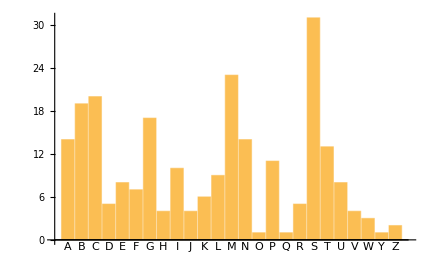
| Expected output: |  
  | -Graphics- |

Find simpler code for 
Grid[Table[StringJoin[TextString[i],"^",TextString[j],"=",TextString[i^j]],{i,5},{j,5}]]. »

| Expected output: |  
  | "1^1=1" | "1^2=1" | "1^3=1" | "1^4=1" | "1^5=1"
"2^1=2" | "2^2=4" | "2^3=8" | "2^4=16" | "2^5=32"
"3^1=3" | "3^2=9" | "3^3=27" | "3^4=81" | "3^5=243"
"4^1=4" | "4^2=16" | "4^3=64" | "4^4=256" | "4^5=1024"
"5^1=5" | "5^2=25" | "5^3=125" | "5^4=625" | "5^5=3125" |

Q&A

How should one read ~~ out loud?

It’s usually read “tilde tilde”. The underlying function is StringExpression.

How does one type `` to make a slot in a string template?

It’s a pair of what are usually called backquote or backtick characters. On many keyboards, they’re at the top left, along with ~ (tilde).

Can I write rules for understanding natural language?

Yes, but we didn’t cover that here. The key function is GrammarRules.

What does TextString do when things don’t have an obvious textual form?

It does its best to make something human readable, but if all else fails, it’ll fall back on InputForm.

Tech Notes

There’s a correspondence between patterns for strings, and patterns for sequences in lists. SequenceCases is the analog for lists of StringCases for strings.

The option Overlaps specifies whether or not to allow overlaps in string matching. Different functions have different defaults.

String patterns by default match longest sequences, so you need to specify Shortest if you want it. Expression patterns by default match shortest sequences.

Among string pattern constructs are Whitespace, NumberString, WordBoundary, StartOfLine, EndOfLine, StartOfString and EndOfString.

Anywhere in a Wolfram Language symbolic string pattern, you can use RegularExpression to include regular expression syntaxes like x* and [abc][def].

TextString tries to make a simple human-readable textual version of anything, dropping things like the details of graphics. ToString[InputForm[expr]] gives a complete version, suitable for subsequent input.

You can compare strings using operations like SequenceAlignment. This is particularly useful in bioinformatics.

FileTemplate, XMLTemplate and NotebookTemplate let you do the analog of StringTemplate for files, XML (and HTML) documents and notebooks.

The Wolfram Language includes the function TextSearch, for searching text in large collections of files.

More to Explore

Guide to String Patterns in the Wolfram Language »